```mathematica
Global Conditions
```

Conditions Global

```mathematica
Clear["Global`*"]
e1=0.01;
e2=0.01;
r=3;
ϵ=(1-e1)*(1-e2)+e1*e2;
e=e2;
(*ternary coords where x corresponds to freq alld, y to freq allc *)
TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.015;
textoffset=.05;
thickness=.005;
vlabels={Graphics[Text["AllD",{-textoffset,-textoffset}]],Graphics[Text["AllC",{1+textoffset,-textoffset}]],Graphics[Text["Disc",{1/2,Tan[Pi/3]/2+textoffset}]]};
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/figures"];
```

```mathematica
Clear["Global`*"]
w12=g; 
w15=g;
w17=g*(1-ϵ);
w18=g*(1-ϵ)*g;
w1=Together[FullSimplify[(w15+w17+w18)/(w12+w15+w17+w18)]]
```

(-2-g+ϵ+g ϵ)/(-3-g+ϵ+g ϵ)

```mathematica
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]]
```

1-e^2/(1+2 e+x gx[t]+y gy[t]-(-1+x+y) gz[t])+(1-e)/(-3+ϵ+x (-1+ϵ) gx[t]+y (-1+ϵ) gy[t]-(-1+x+y) (-1+ϵ) gz[t])

```mathematica
Simple Standing
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
w12=g; 
w15=g;
w17=g*(1-ϵ);
w18=g*(1-ϵ)*g;
w1=FullSimplify[(w15+w17+w18)/(w12+w15+w17+w18)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w32=e*g; 
w35=g*e;
w37=g;
w38=g^2;
w3=Simplify[(w35+w37+w38)/(w32+w35+w37+w38)];
(* World 4: B -> G *)
w42=e; 
w45=g*e*(1-g);
w47=g*(1-g);
w48=g;
w4=Simplify[(w45+w47+w48)/(w42+w45+w47+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=1-g; 
w65=1-g;
w67=(1-ϵ)*(1-g);
w68=1-ϵ;
w6=Simplify[(w65+w67+w68)/(w62+w65+w67+w68)];
(* World 7: G -> G *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{66,5}];
count=1;
Do[
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
gx20=gx0*RandomReal[];
gy20=gy0*RandomReal[];
gz20=gz0*RandomReal[];
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==gx0,gy[0]==gy0,gz[0]==gz0,gx2[0]==gx20,gy2[0]==gy20,gz2[0]==gz20}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSAbductive=Show[ternplot,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["SS_Abductive.pdf",imageSSAbductive];
```

Simple Standing

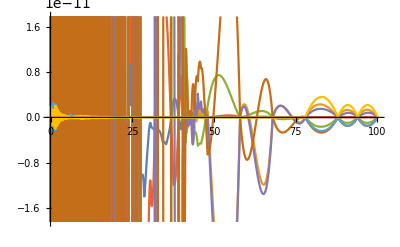

```mathematica
g=x[t]*gx[t]+y[t]*gy[t]+(1-x[t]-y[t])*gz[t];
g2=x[t]*gx2[t]+y[t]*gy2[t]+(1-x[t]-y[t])*gz2[t];
(* World 1: B ∅ B *)
w12=g; 
w15=g;
w17=g*(1-ϵ);
w18=g*(1-ϵ)*g;
w1=FullSimplify[(w15+w17+w18)/(w12+w15+w17+w18)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w32=e*g; 
w35=g*e;
w37=g;
w38=g^2;
w3=Simplify[(w35+w37+w38)/(w32+w35+w37+w38)];
(* World 4: B -> G *)
w42=e; 
w45=g*e*(1-g);
w47=g*(1-g);
w48=g;
w4=Simplify[(w45+w47+w48)/(w42+w45+w47+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=1-g; 
w65=1-g;
w67=(1-ϵ)*(1-g);
w68=1-ϵ;
w6=Simplify[(w65+w67+w68)/(w62+w65+w67+w68)];
(* World 7: G -> G *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
pix=r*(x[t]+gx[t]*(1-x[t]-y[t]))-1;
piy=r*(x[t]+gy[t]*(1-x[t]-y[t]));
piz=r*(x[t]+gz[t]*(1-x[t]-y[t]))-(gx[t]*x[t]+gy[t]*y[t]+gz[t]*(1-x[t]-y[t]));
pi=x[t]*pix+y[t]*piy+(1-x[t]-y[t])*piz;
xdot=x[t]*(pix-pi);
ydot=y[t]*(piy-pi);
repsys1={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t],
x'[t]==0.00001*xdot,
y'[t]==0.00001*ydot
};
R=NDSolve[Join[repsys1,{gx[0]==gx0,gy[0]==gy0,gz[0]==gz0,gx2[0]==gx20,gy2[0]==gy20,gz2[0]==gz20,x[0]==0.4,y[0]==0.2}],{gx,gy,gz,gx2,gy2,gz2,x,y},{t,0,100}];
Plot[Evaluate[repsys1/.R],{t,0,100}]
```

```mathematica
Shunning
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
w1=0;
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w41=e*(1-g); 
w42=e;
w43=1-g;
w48=g;
w4=Simplify[w48/(w41+w42+w43+w48)];
(* World 5: G ∅ B *)
w51=1-g; 
w52=(1-g)*g;
w53=(1-g)*(1-ϵ);
w58=(1-ϵ)*g;
w5=Simplify[w58/(w51+w52+w53+w58)];
(* World 6: G ∅ G *)
w61=(1-g)^2; 
w62=1-g;
w63=(1-g)*(1-ϵ)*(1-g);
w68=1-ϵ;
w6=Simplify[w68/(w61+w62+w63+w68)];
(* World 7: G -> B *)
w71=(1-g)*e; 
w72=(1-g)*e;
w73=1-g;
w78=g^2;
w7=Simplify[w78/(w71+w72+w73+w78)];
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{66,5}];
count=1;
Do[
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
gx20=gx0*RandomReal[];
gy20=gy0*RandomReal[];
gz20=gz0*RandomReal[];
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==gx0,gy[0]==gy0,gz[0]==gz0,gx2[0]==gx20,gy2[0]==gy20,gz2[0]==gz20}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageShAbductive=Show[ternplot,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["Sh_Abductive.pdf",imageShAbductive];
```

```mathematica
Stern Judging
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
w12=g; 
w13=1-ϵ;
w15=g;
w18=g*(1-ϵ)*g;
w1=Simplify[(w15+w18)/(w12+w13+w15+w18)];
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w3=0;
(* World 4: B -> G *)
w42=e; 
w43=1-g;
w45=g*e*(1-g);
w48=g;
w4=Simplify[(w45+w48)/(w42+w43+w45+w48)];
(* World 5: G ∅ B *)
w5=1;
(* World 6: G ∅ G *)
w62=1-g; 
w63=(1-g)*(1-ϵ)*(1-g);
w65=(1-g);
w68=1-ϵ;
w6=Simplify[(w65+w68)/(w62+w63+w65+w68)];
(* World 7: G -> B *)
w72=(1-g)*e*g; 
w73=1-g;
w75=e;
w78=g;
w7=Simplify[(w75+w78)/(w72+w73+w75+w78)];
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{66,5}];
count=1;
Do[
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
gx20=gx0*RandomReal[];
gy20=gy0*RandomReal[];
gz20=gz0*RandomReal[];
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==gx0,gy[0]==gy0,gz[0]==gz0,gx2[0]==gx20,gy2[0]==gy20,gz2[0]==gz20}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJAbductive=Show[ternplot,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["SJ_Abductive.pdf",imageSJAbductive];
```

```mathematica
Scoring
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* World 1: B ∅ B *)
w1=0;
(* World 2: B ∅ G *)
w2=0;
(* World 3: B -> B *)
w31=e; 
w32=e*g;
w37=g;
w38=g^2;
w3=Simplify[(w37+w38)/(w31+w32+w37+w38)];
(* World 4: B -> G *)
w41=e*(1-g); 
w42=e;
w47=g*(1-g);
w48=g;
w4=Simplify[(w47+w48)/(w41+w42+w47+w48)];
(* World 5: G ∅ B *)
w51=(1-g)*(1-e); 
w52=(1-g)*g;
w57=1-ϵ;
w58=(1-ϵ)*g;
w5=Simplify[(w47+w48)/(w41+w42+w47+w48)];
(* World 6: G ∅ G *)
w61=(1-g)*(1-g); 
w62=1-g;
w67=(1-ϵ)*(1-g);
w68=1-ϵ;
w6=Simplify[(w67+w68)/(w61+w62+w67+w68)];
(* World 7: G -> G *)
w7=1;
(* World 8: G -> G *)
w8=1;
Qbdb=FullSimplify[Together[(1-e)*w1+e*w3]];
Qbdg=FullSimplify[Together[(1-e)*w2+e*w4]];
Qbcb=FullSimplify[Together[ϵ*w3+(1-ϵ)*w1]];
Qbcg=FullSimplify[Together[ϵ*w4+(1-ϵ)*w2]];
Qgdb=FullSimplify[Together[(1-e)*w5+e*w7]];
Qgdg=FullSimplify[Together[(1-e)*w6+e*w8]];
Qgcb=FullSimplify[Together[ϵ*w7+(1-ϵ)*w5]];
Qgcg=FullSimplify[Together[ϵ*w8+(1-ϵ)*w6]];
repsys={
gx'[t]==(Qbcg*g+Qbcb*(1-g))-(1+(Qbcg-Qgcg)*g+(Qbcb-Qgcb)*(1-g))*gx[t],
gy'[t]==(Qbdg*g+Qbdb*(1-g))-(1+(Qbdg-Qgdg)*g+(Qbdb-Qgdb)*(1-g))*gy[t],
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2g+g2))-gz[t]*((1-Qbcg)*g2+(2-Qbcb-Qbdg)*(g-g2)+(1-Qbdb)*(1-2*g+g2)),
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{66,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageScAbductive=Show[ternplot,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["Sc_Abductive.pdf",imageScAbductive];
```